```mathematica
Lx=100
Ly=100;
A=Lx*Ly;
```

100

```mathematica
m0 = 0.5;
```

```mathematica
LineChernListP1 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m0=0.25Xup=22Xdn=12PartsPerThousand=106Irrational.dat"];
```

```mathematica
LineChernListP2 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m0=-0.25Xup=22Xdn=12PartsPerThousand=106Irrational.dat"];
```

```mathematica
list1 = Table[LineChernListP1[[ii]][[3]],{ii,1,Lx}]
```

{-13.0212,-6.89144,-3.4854,-1.61968,-0.449526,0.14692,0.526633,0.71247,0.816748,0.884327,0.917593,0.938434,0.950444,0.956247,0.959139,0.961716,0.962154,0.96419,0.964491,0.963421,0.964151,0.963484,0.964254,0.964125,0.961961,0.964091,0.964192,0.963458,0.964146,0.96346,0.964197,0.964099,0.961975,0.964148,0.964293,0.963569,0.964295,0.963667,0.964927,0.964928,0.963669,0.964299,0.963576,0.964305,0.964167,0.962004,0.964167,0.964305,0.963576,0.964299,0.963669,0.964928,0.964927,0.963667,0.964295,0.963569,0.964293,0.964149,0.961975,0.9641,0.964197,0.96346,0.964147,0.96346,0.964197,0.9641,0.961975,0.964148,0.964293,0.963568,0.964294,0.963665,0.964924,0.964922,0.963658,0.964282,0.963546,0.964249,0.964075,0.961849,0.963859,0.963788,0.96266,0.962788,0.961134,0.959809,0.956629,0.947407,0.939351,0.921741,0.884737,0.829463,0.730366,0.525416,0.20574,-0.412133,-1.41279,-3.22582,-6.53177,-12.4584}

```mathematica
list2 = Table[LineChernListP2[[ii]][[3]],{ii,1,Lx}]
```

{13.0212,6.89144,3.4854,1.61968,0.449526,-0.14692,-0.526633,-0.71247,-0.816748,-0.884327,-0.917593,-0.938434,-0.950444,-0.956247,-0.959139,-0.961716,-0.962154,-0.96419,-0.964491,-0.963421,-0.964151,-0.963484,-0.964254,-0.964125,-0.961961,-0.964091,-0.964192,-0.963458,-0.964146,-0.96346,-0.964197,-0.964099,-0.961975,-0.964148,-0.964293,-0.963569,-0.964295,-0.963667,-0.964927,-0.964928,-0.963669,-0.964299,-0.963576,-0.964305,-0.964167,-0.962004,-0.964167,-0.964305,-0.963576,-0.964299,-0.963669,-0.964928,-0.964927,-0.963667,-0.964295,-0.963569,-0.964293,-0.964149,-0.961975,-0.9641,-0.964197,-0.96346,-0.964147,-0.96346,-0.964197,-0.9641,-0.961975,-0.964148,-0.964293,-0.963568,-0.964294,-0.963665,-0.964924,-0.964922,-0.963658,-0.964282,-0.963546,-0.964249,-0.964075,-0.961849,-0.963859,-0.963788,-0.96266,-0.962788,-0.961134,-0.959809,-0.956629,-0.947407,-0.939351,-0.921741,-0.884737,-0.829463,-0.730366,-0.525416,-0.20574,0.412133,1.41279,3.22582,6.53177,12.4584}

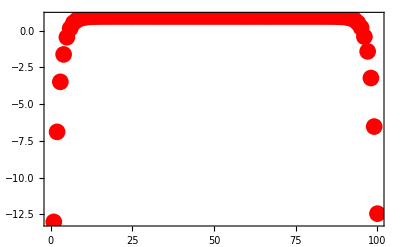

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

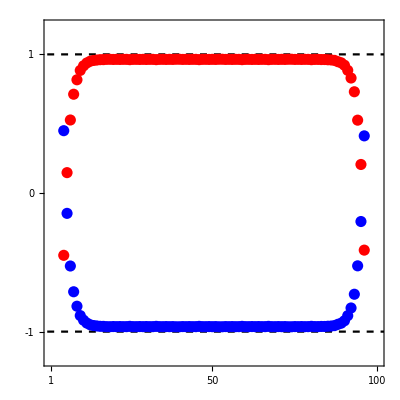

```mathematica
Show[Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
ListPlot[list1,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{0,"0"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1]
```